{{x→(-d1y+d2y+d1x m1-d2x m2)/(m1-m2)}}

{{x→(-d2y+d3y+d2x m2-d3x m3)/(m2-m3)}}

(-d2y+d3y+d2x m2-d3x m3)/(m2-m3)

{{x→(-d1y+d3y+d1x m1-d3x m3)/(m1-m3)}}

{5,6}

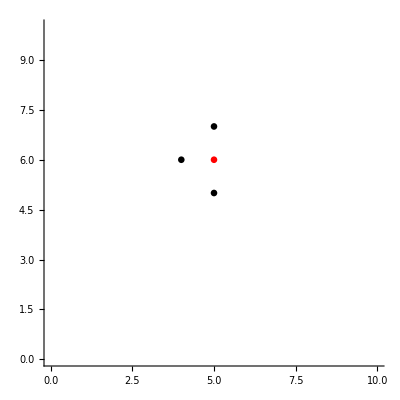

```mathematica
ClearAll["Global`*"];
nRad=.1;
pA={Ax,Ay};
pB={Bx,By};
pC={Cx,Cy};

y1[x_]:=m1(x-d1x)+d1y;
y2[x_]:=m2(x-d2x)+d2y;
y3[x_]:=m3(x-d3x)+d3y;
Solve[y1[x]==y2[x],x]
S=Solve[y2[x]==y3[x],x]
Px=S[[1]][[1]][[2]]
Py=y2[Px];
pP={Px,Py};

Solve[y1[x]==y3[x],x]

m1=-(Ax-Bx)/(Ay-By);
m2=-(Bx-Cx)/(By-Cy);
m3=-(Cx-Ax)/(Cy-Ay);

{d1x,d1y}={(Ax+Bx)/2,(Ay+By)/2};
{d2x,d2y}={(Bx+Cx)/2,(By+Cy)/2};
{d3x,d3y}={(Cx+Ax)/2,(Cy+Ay)/2};

{Ax,Ay}={5,5};
{Bx,By}={5,7};
{Cx,Cy}={4,6};

dA=Graphics[{Black,Disk[pA,nRad]}];
dB=Graphics[{Black,Disk[pB,nRad]}];
dC=Graphics[{Black,Disk[pC,nRad]}];
dP=Graphics[{Red,Disk[pP,nRad]}];
pP
Show[
dA,dB,dC,dP,
Axes->True,
AspectRatio->Automatic,
PlotRange->{{0,10},{0,10}}
]
```

```mathematica
(-((Ax-Bx) d1x)/(Ay-By)-d1y+((Bx-Cx) d2x)/(By-Cy)+d2y)/(-(Ax-Bx)/(Ay-By)+(Bx-Cx)/(By-Cy))
```